{{n→-1466.6},{n→1466.6}}

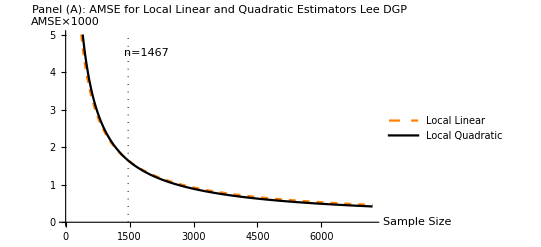

```mathematica
(* Panel (A): Lee DGP *)
tauY=0.52-0.48; (*true treatment effect*)
betaYr=0.84; (*coefficients for the conditional expectation functions*)
betaYl=1.27;
beta2Yr=-3.00;
beta2Yl=7.18;
beta3Yr=7.99;
beta3Yl=20.21;
beta4Yr=-9.01;
beta4Yl=21.54;
beta5Yr=3.56;
beta5Yl=7.33;
sigma2Yr=0.1295^2; (*conditional variance*)
sigma2Yl=0.1295^2;
f0=0.625; (*density of running variable at cutoff*)
DLn=6558;(*sample size*)
kernelT[u_]:=1-Abs[u](*kernel*)
GammaT1=({{Integrate[kernelT[u],{u,0,1}], Integrate[u kernelT[u],{u,0,1}]}, {Integrate[u kernelT[u],{u,0,1}], Integrate[u^2 kernelT[u],{u,0,1}]}});(*matrices of kernel constants for LL estimator*)
PsiT1=({{Integrate[kernelT[u]^2,{u,0,1}], Integrate[u kernelT[u]^2,{u,0,1}]}, {Integrate[u kernelT[u]^2,{u,0,1}], Integrate[u^2 kernelT[u]^2,{u,0,1}]}});
varpsilonT1=({{Integrate[u^2 kernelT[u],{u,0,1}]}, {Integrate[u^3 kernelT[u],{u,0,1}]}});
BT1=(beta2Yr-beta2Yl) (Inverse[GammaT1].varpsilonT1)[[1]][[1]];(*B1*)
VT1=(sigma2Yr+sigma2Yl)/f0 (Inverse[GammaT1].PsiT1.Inverse[GammaT1])[[1]][[1]];(*V1*)
ConsT1=VT1/(4 BT1^2);(*constant for bandwidth calculation*)
hT1[n_]:=ConsT1^(1/5)n^(-1/5)(*LL bandwidth as a function of sample size*)
AMSET1[n_,h_]:=BT1^2 h^4+1/(n h)VT1(*AMSE of the LL estimator*)
(*analogous definitions for the LQ estimator*)
GammaT2=({{Integrate[kernelT[u],{u,0,1}], Integrate[u kernelT[u],{u,0,1}], Integrate[u^2 kernelT[u],{u,0,1}]}, {Integrate[u kernelT[u],{u,0,1}], Integrate[u^2 kernelT[u],{u,0,1}], Integrate[u^3 kernelT[u],{u,0,1}]}, {Integrate[u^2 kernelT[u],{u,0,1}], Integrate[u^3 kernelT[u],{u,0,1}], Integrate[u^4 kernelT[u],{u,0,1}]}});
PsiT2=({{Integrate[kernelT[u]^2,{u,0,1}], Integrate[u kernelT[u]^2,{u,0,1}], Integrate[u^2 kernelT[u]^2,{u,0,1}]}, {Integrate[u kernelT[u]^2,{u,0,1}], Integrate[u^2 kernelT[u]^2,{u,0,1}], Integrate[u^3 kernelT[u]^2,{u,0,1}]}, {Integrate[u^2 kernelT[u]^2,{u,0,1}], Integrate[u^3 kernelT[u]^2,{u,0,1}], Integrate[u^4 kernelT[u]^2,{u,0,1}]}});
varpsilonT2=({{Integrate[u^3 kernelT[u],{u,0,1}]}, {Integrate[u^4 kernelT[u],{u,0,1}]}, {Integrate[u^5 kernelT[u],{u,0,1}]}});
BT2=(beta3Yr+beta3Yl) (Inverse[GammaT2].varpsilonT2)[[1]][[1]];
VT2=(sigma2Yr+sigma2Yl)/f0 (Inverse[GammaT2].PsiT2.Inverse[GammaT2])[[1]][[1]];
ConsT2=VT2/(6 BT2^2);
hT2[n_]:=ConsT2^(1/7)n^(-1/7)
AMSET2[n_,h_]:=BT2^2 h^6+1/(n h)VT2
NSolve[AMSET2[n,hT2[n]]==AMSET1[n,hT1[n]],n]
vertical=Line[{{1467,0},{1467,5}}];
AMSELee=Plot[{1000*AMSET1[n,hT1[n]],1000*AMSET2[n,hT2[n]]},{n,100,7200},PlotStyle->{{Dashed,Orange},{Black}},PlotLabel->"Panel (A): AMSE for Local Linear and Quadratic Estimators\n Lee DGP",BaseStyle->{FontFamily->"Times"},AxesLabel->{"Sample\nSize","AMSE×1000"},PlotRange->{{0,7200},{0,5}},PlotLegends->Placed[{"Local Linear","Local Quadratic"},Scaled[{0.7,0.6}]],Epilog->{Directive[Dotted],vertical,Text["n=1467",{1900,4.5}]}]
```

```mathematica
(*Export["C:/Users/zp53/Dropbox/local poly/graphs/RD AMSE Lee jbes.pdf",AMSELee, ImageSize->Medium];*)
```

{{n→1.04113}}

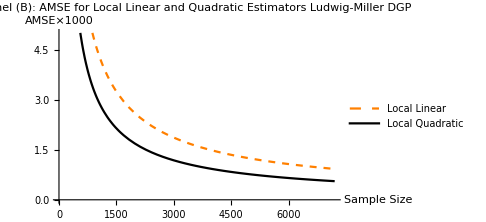

```mathematica
(* Panel (B): LM DGP *)
tauY=0.26-3.71;
betaYr=18.49;
betaYl=2.30;
beta2Yr=-54.81;
beta2Yl=3.28;
beta3Yr=74.30;
beta3Yl=1.45;
beta4Yr=-45.02;
beta4Yl=0.23;
beta5Yr=9.83;
beta5Yl=0.03;
sigma2Yr=0.1295^2;
sigma2Yl=0.1295^2;
f0=0.625;
BT1=(beta2Yr-beta2Yl) (Inverse[GammaT1].varpsilonT1)[[1]][[1]];
VT1=(sigma2Yr+sigma2Yl)/f0 (Inverse[GammaT1].PsiT1.Inverse[GammaT1])[[1]][[1]];
ConsT1=VT1/(4 BT1^2);
hT1[n_]:=ConsT1^(1/5)n^(-1/5)
AMSET1[n_,h_]:=BT1^2 h^4+1/(n h)VT1
BT2=(beta3Yr+beta3Yl) (Inverse[GammaT2].varpsilonT2)[[1]][[1]];
VT2=(sigma2Yr+sigma2Yl)/f0 (Inverse[GammaT2].PsiT2.Inverse[GammaT2])[[1]][[1]];
ConsT2=VT2/(6 BT2^2);
hT2[n_]:=ConsT2^(1/7)n^(-1/7)
AMSET2[n_,h_]:=BT2^2 h^6+1/(n h)VT2
NSolve[AMSET2[n,hT2[n]]==AMSET1[n,hT1[n]],n]
AMSELM=Plot[{1000*AMSET1[n,hT1[n]],1000*AMSET2[n,hT2[n]]},{n,100,7200},PlotStyle->{{Dashed,Orange},{Black}},PlotLabel->"Panel (B): AMSE for Local Linear and Quadratic Estimators\n Ludwig-Miller DGP",BaseStyle->{FontFamily->"Times"},AxesLabel->{"Sample\nSize","AMSE×1000"},PlotRange->{{0,7200},{0,5}},PlotLegends->Placed[{"Local Linear","Local Quadratic"},Scaled[{0.7,0.6}]],ImageSize->Medium]
```

```mathematica
(*Export["C:/Users/zp53/Dropbox/local poly/graphs/RD AMSE LM jbes.pdf",AMSELM, ImageSize->Medium];*)
```

{{n→8.59047×10^7}}

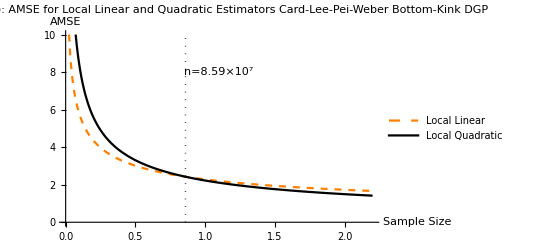

```mathematica
(* Panel (C): CLPW Bottom-Kink DGP *)
tauB=2.3 10^(-5);
tauY=2.99 10^(-5);
beta2Yr=6.9406863301534 10^(-9);
beta2Yl=1.6404416296502×10^(-7);
beta3Yr=-4.5212194831915×10^(-12);
beta3Yl=3.0466820112444×10^(-10);
beta4Yr=1.2746842549552×10^(-15);
beta4Yl=1.8262401385459×10^(-13);
beta5Yr=-1.4623673689342×10^(-19);
beta5Yl=3.5377936220000×10^(-17);
beta2Br=5.2378125231639×10^(-9);
beta2Bl=-1.2124163279348*10^(-8);
beta3Br=-3.8316207698506×10^(-12);
beta3Bl=-1.0109354471178 10^(-11);
beta4Br=9.5393480619799×10^(-16);
beta4Bl=-7.5534624888669*10^(-16);
beta5Br=-8.0207110673716×10^(-20);
beta5Bl=7.8880445708604*10^(-19);
sigma2Yr=1.2272514801761;
sigma2Br=1.4312711837643×10^(-2);
sigmaYBr=-3.1253013995940×10^(-3);
sigma2Yl=1.2193910688403;
sigma2Bl=1.4393072729860×10^(-2);
sigmaYBl=-5.0148450069856×10^(-3);
f=1.5315519484983 10^(-4);
bottomn=275292;
BT1=(1/tauB(beta2Yr+beta2Yl)-tauY/tauB^2(beta2Br+beta2Bl)) (Inverse[GammaT1].varpsilonT1)[[2]][[1]];
VT1=(1/tauB^2 (sigma2Yr+sigma2Yl)/f-(2 tauY)/tauB^3(sigmaYBr+sigmaYBl)/f+tauY^2/tauB^4 (sigma2Br+sigma2Bl)/f) (Inverse[GammaT1].PsiT1.Inverse[GammaT1])[[2]][[2]];
ConsT1=(3 VT1)/(2 BT1^2);
hT1[n_]:=ConsT1^(1/5)n^(-1/5)
AMSE1[n_,h_]:=BT1^2 h^2+1/(n h^3)VT1
BT2=(1/tauB(beta3Yr-beta3Yl)-tauY/tauB^2(beta3Br-beta3Bl)) (Inverse[GammaT2].varpsilonT2)[[2]][[1]];
VT2=(1/tauB^2 (sigma2Yr+sigma2Yl)/f-(2 tauY)/tauB^3(sigmaYBr+sigmaYBl)/f+tauY^2/tauB^4 (sigma2Br+sigma2Bl)/f) (Inverse[GammaT2].PsiT2.Inverse[GammaT2])[[2]][[2]];
ConsT2=(3 VT2)/(4 BT2^2);
hT2[n_]:=ConsT2^(1/7)n^(-1/7)
AMSE2[n_,h_]:=BT2^2 h^4+1/(n h^3)VT2
NSolve[AMSE2[n,hT2[n]]==AMSE1[n,hT1[n]],n]
vertical=Line[{{8.590467796667907*^7,0},{8.590467796667907*^7,10}}];
AMSEKink3=Plot[{AMSE1[n,hT1[n]],AMSE2[n,hT2[n]]},{n,10000,220000000},PlotStyle->{{Dashed,Orange},{Black}},PlotLabel->"Panel (C): AMSE for Local Linear and Quadratic Estimators\n Card-Lee-Pei-Weber Bottom-Kink DGP",BaseStyle->{FontFamily->"Times"},AxesLabel->{"Sample\nSize","AMSE"},PlotRange->{{10000,220000000},{0,10}},PlotLegends->Placed[{"Local Linear","Local Quadratic"},Scaled[{0.75,0.5}]],Epilog->{Directive[Dotted],vertical,Text["n=8.59×10^7",{110000000,8}]}]
```

```mathematica
(*Export["C:/Users/zp53/Dropbox/local poly/graphs/RD AMSE Kink3 jbes.pdf",AMSEKink3, ImageSize->Medium];*)
```

{{n→5.9878×10^13}}

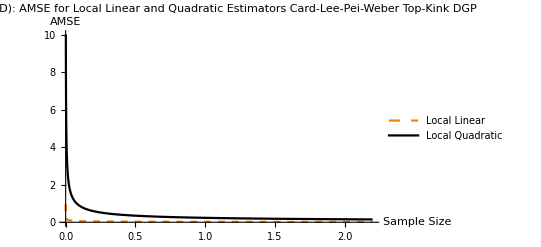

```mathematica
(* Panel (D): CLPW Bottom-Kink DGP *)
tauB=-1.4*10^(-5);
tauY=-2.8*10^(-5);
beta0=4.6461;
beta1Yl=0.0000151;
beta1Yr=beta1Yl+tauY;
beta2Yr=2.3464979188637 10^(-8);
beta2Yl=-5.6888924692040×10^(-9);
beta3Yr=-1.4190347966551×10^(-11);
beta3Yl=-1.0749283115500×10^(-12);
beta4Yr=3.0385421157658×10^(-15);
beta4Yl=-8.4915826796722×10^(-17);
beta5Yr=-2.0572980507244×10^(-19);
beta5Yl=-2.6496893621844×10^(-21);
beta2Br=1.2519142200344×10^(-8);
beta2Bl=-3.1758450254165*10^(-9);
beta3Br=-6.1711254813928×10^(-12);
beta3Bl=-5.7202427897121*10^(-13);
beta4Br=1.1636415370651×10^(-15);
beta4Bl=-4.8286924635476*10^(-17);
beta5Br=-7.4287243049336×10^(-20);
beta5Bl=-1.4171464182077*10^(-21);
sigma2Yr=1.2714993239029;
sigma2Br=3.4589743763015×10^(-2);
sigmaYBr=-1.0105548371891×10^(-3);
sigma2Yl=1.2770061698100;
sigma2Bl=3.0983092379928×10^(-2);
sigmaYBl=-6.7639691045137×10^(-3);
f=2.3509547388472 10^(-5);
BT1=(1/tauB(beta2Yr+beta2Yl)-tauY/tauB^2(beta2Br+beta2Bl)) (Inverse[GammaT1].varpsilonT1)[[2]][[1]];
VT1=(1/tauB^2 (sigma2Yr+sigma2Yl)/f-(2 tauY)/tauB^3(sigmaYBr+sigmaYBl)/f+tauY^2/tauB^4 (sigma2Br+sigma2Bl)/f) (Inverse[GammaT1].PsiT1.Inverse[GammaT1])[[2]][[2]];
ConsT1=(3 VT1)/(2 BT1^2);
hT1[n_]:=ConsT1^(1/5)n^(-1/5)
AMSE1[n_,h_]:=BT1^2 h^2+1/(n h^3)VT1
BT2=(1/tauB(beta3Yr-beta3Yl)-tauY/tauB^2(beta3Br-beta3Bl)) (Inverse[GammaT2].varpsilonT2)[[2]][[1]];
VT2=(1/tauB^2 (sigma2Yr+sigma2Yl)/f-(2 tauY)/tauB^3(sigmaYBr+sigmaYBl)/f+tauY^2/tauB^4 (sigma2Br+sigma2Bl)/f) (Inverse[GammaT2].PsiT2.Inverse[GammaT2])[[2]][[2]];
ConsT2=(3 VT2)/(4 BT2^2);
hT2[n_]:=ConsT2^(1/7)n^(-1/7)
AMSE2[n_,h_]:=BT2^2 h^4+1/(n h^3)VT2
NSolve[AMSE2[n,hT2[n]]==AMSE1[n,hT1[n]],n]
vertical=Line[{{5.987800693046686*^13,0},{5.987800693046686*^13,10}}];
AMSEKink4=Plot[{AMSE1[n,hT1[n]],AMSE2[n,hT2[n]]},{n,10000,220000000},PlotStyle->{{Dashed,Orange},{Black}},PlotLabel->"Panel (D): AMSE for Local Linear and Quadratic Estimators\n Card-Lee-Pei-Weber Top-Kink DGP",BaseStyle->{FontFamily->"Times"},AxesLabel->{"Sample\nSize","AMSE"},PlotRange->{{10000,220000000},{0,10}},PlotLegends->Placed[{"Local Linear","Local Quadratic"},Scaled[{0.75,0.5}]],Epilog->{Directive[Dotted],vertical,Text["n=5.99×10^13",{7×10^13,8}]}]
```

```mathematica
(*Export["C:/Users/zp53/Dropbox/local poly/graphs/RD AMSE Kink4 jbes.pdf",AMSEKink4, ImageSize->Medium];*)
```